```mathematica
DSolve[y'''[x]+-((8*((y'[x])^2))/((y[x])^2))-(((24/25)*16*9)*(((y[x])^2)/((y'[x])^2)))==0,y[x],x]
```

DSolve[-(3456 y[x]^2)/(25 y'[x]^2)-(8 y'[x]^2)/y[x]^2+(10 y''[x])/y[x]+y^(3)[x]==0,y[x],x]

```mathematica
DSolve[(y''[x]/2)-((y'[x]^2)/y[x])+(Pi/25)*y[x]==0,y[x],x]
```

{{y[x]→C[2] Sech[1/5 √(2 π) (x-25 C[1])]}}

{{y[x]→ⅇ^(-1/5 √6 (-x+(5 Log[1+ⅇ^(2/5 √6 (x+25 C[1]))])/(√6))) C[2]}}

ⅇ^(x/(5 √2))

ⅇ^(x/(5 √2))/(5 √2)

1/50 ⅇ^(x/(5 √2))

(3 (ⅇ^((√2 x)/5)-ⅇ^((√2 x)/5)/(200 π)))/(8 π)

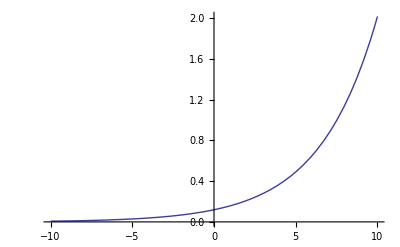

1/50

1/50

24/25

```mathematica
DSolve[(y''[x]/2)-((y'[x]^2)/y[x])+(3/25)*y[x]==0,y[x],x]
(*solution = Exp[((Sqrt[6]/5)*x)-Log[1+Exp[((2*Sqrt[6])/3)*x]]]*)
(*solution = 1/x*)
(*solution = Sech[1/5 Sqrt[2*Pi]*(x-25)]*)
solution = Exp[x/(5*Sqrt[2])]
firstderiv = D[solution,x]
secondderiv = D[firstderiv,x]
(*Vphi = ((3*(m^2))/(8*pi))*((solution^2)-((3*m^2)/(12*pi))*(firstderiv^2))*)
Vphi = ((3)/(8*Pi))*((solution^2)-((3)/(12*Pi))*(firstderiv^2))
Plot[Vphi,{x,-10,10}]
etaH = secondderiv/solution
epsilonH = (firstderiv/solution)^2
ns = (2*etaH)-(4*epsilonH)+1
```